# Exponential

```mathematica
dist=ExponentialDistribution[λ]
```

ExponentialDistribution[λ]

```mathematica
PDF[dist,z]
```

Piecewise[{{ⅇ^(-z λ) λ, z≥0}, {0, True}}]

```mathematica
CDF[dist,z]
```

Piecewise[{{1-ⅇ^(-z λ), z≥0}, {0, True}}]

```mathematica
Manipulate[Plot[PDF[ExponentialDistribution[λ],x],{x,0,3},Filling->Axis,PlotRange->All],{λ,1/2,2}]
```

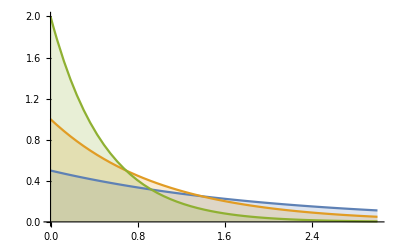

```mathematica
Plot[Table[PDF[ExponentialDistribution[λ],x],{λ,{1/2,1,2}}]//Evaluate,{x,0,3},Filling->Axis,PlotRange->All]
```

```mathematica
Mean[dist]
```

1/λ

```mathematica
Median[dist]
```

Log[2]/λ

```mathematica
Variance[dist]
```

1/λ^2

```mathematica
StandardDeviation[dist]
```

1/λ

```mathematica
Skewness[dist]
```

2

```mathematica
Kurtosis[dist]
```

9

```mathematica
CharacteristicFunction[dist,t]
```

λ/(-ⅈ t+λ)

```mathematica
Random[ExponentialDistribution[1]]
```

0.0675176